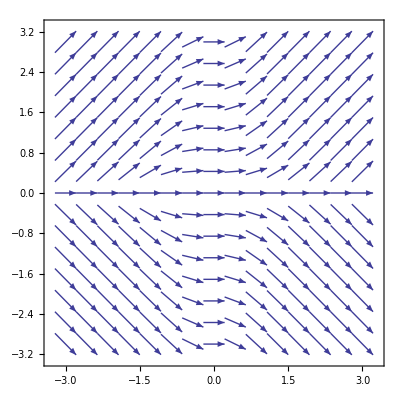

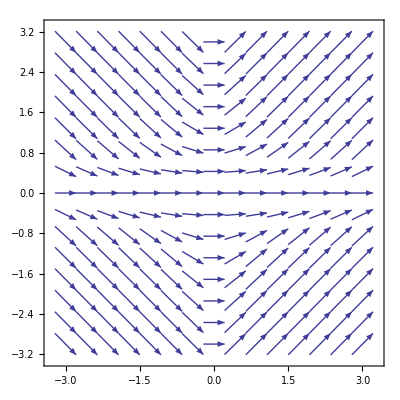

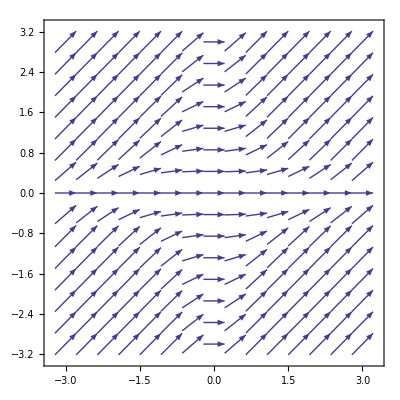

```mathematica
correctSlopeF=VectorPlot[{1,x^2*y/Sqrt[1+ x^4y^2]},{x,-3,3},{y,-3,3}]
incorrectSlopeF1=VectorPlot[{1,x*y^2/Sqrt[1+ x^2y^4]},{x,-3,3},{y,-3,3}]
incorrectSlopeF2=VectorPlot[{1,x^2*y^2/Sqrt[1+ x^4y^4]},{x,-3,3},{y,-3,3}]
```

```mathematica
Export["correctSlopeF.png", correctSlopeF]
Export["incorrectSlopeF1.png", incorrectSlopeF1]
Export["incorrectSlopeF2.png", incorrectSlopeF2]
```

correctSlopeF.png

incorrectSlopeF1.png

incorrectSlopeF2.png

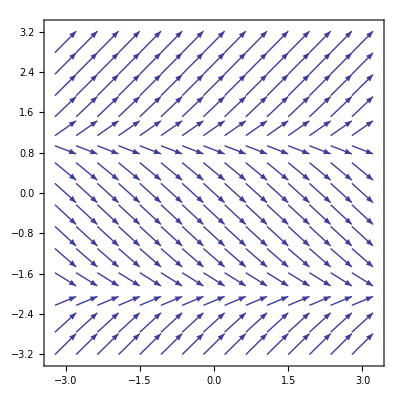

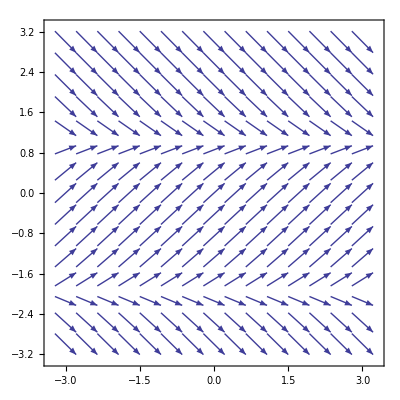

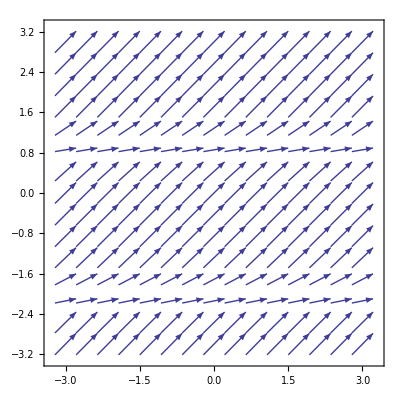

```mathematica
anotherCorrectSlopeF=VectorPlot[{1,(y-1)(y+2)/Sqrt[1+ ((y-1)(y+2))^2]},{x,-3,3},{y,-3,3}]
anotherIncorrectSlopeF1=VectorPlot[{1,-(y-1)(y+2)/Sqrt[1+ ((y-1)(y+2))^2]},{x,-3,3},{y,-3,3}]
anotherIncorrectSlopeF2=VectorPlot[{1,(y-1)^2(y+2)^2/Sqrt[1+ ((y-1)^2(y+2)^2)^2]},{x,-3,3},{y,-3,3}]
```

```mathematica
Export["anotherCorrectSlopeF.png", anotherCorrectSlopeF]
Export["anotherIncorrectSlopeF1.png", anotherIncorrectSlopeF1]
Export["anotherIncorrectSlopeF2.png", anotherIncorrectSlopeF2]
```

anotherCorrectSlopeF.png

anotherIncorrectSlopeF1.png

anotherIncorrectSlopeF2.png